# Finding a Parametrization for the Rough Diffuse Surface Simulation

We wrote a program that is capable of generating or loading a microsurface and ray-tracing that surface using a very large amount of rays (several hundred millions), thus obtaining the distribution of outgoing directions after 1 or more scattering events (up to 4).
We gathered the outgoing lobes for different parameters of the surface:
	• Angle of incidence
	• Roughness
	• Albedo

We then performed a fitting of the simulated data using a modified cosine lobel model that uses non-uniform scaling and a local tangent space.
The matrix M allows to transform from local lobe space to surface space:

	A=(T
B
σ_n R(θ_l))
	ω_w= (ω_l ·A)/(|ω_l ·A|)
	ω_l= (ω_w· A^-1)/(|ω_w ·A^-1|)
	
ω_l is the local lobe-space unit vector
ω_w is the surface-space unit vector after renormalization
R(θ_l) is the lobe’s principal axis (usually, the reflected incoming direction). It’s defined by one of the parameters of the lobe model θ_l
T, B are the complementary vectors forming an orthonormal basis with N
σ_n is a non-uniform scaling factor along the lobe’s principal direction and another one of the parameters of the lobe model

#### Lobe Intensity in Local-Space, Given Two Directions in Surface-Space

Once in local lobe-space, the intensity of the lobe is given by:

	f(ω_o,ω_i,ρ,σ,μ) = σ [(1-μ) + μ G(ω_o·Z,ρ) G(ω_i·Z,ρ)] N( ω_i, ρ )
	
	G(θ,ρ) = Piecewise[{{(3.535 a + 2.181 a^2)/(1.0 + 2.276 a + 2.577 a^2), a(θ,ρ) < 1.6}, {1, otherwise}}]
	a(θ,ρ) = (√(1+(α(ρ))/2))/(tan(θ))
	N( ω_i, ρ ) =  (2+α(ρ))/π [(ω_i ·A^-1)/(|ω_i ·A^-1|).Z]^(α(ρ))	
	α(ρ)= 2^(10(1-ρ))-1
	
	ω_o is the outgoing view direction in surface space
	ω_i is the incoming light direction in surface space
	σ is the global scale factor
	μ is the masking importance factor in [0,1] that allows to bypass the masking term (μ=0) completely.
	G(θ,ρ) is the masking term for the Phong model
	N( ω_i, ρ ) defines the cosine lobe’s intensity using roughness, angle from local normal axis and global scale
	α(ρ) defines the exponent based on the surface’s roughness (notice the -1 in the end that allows use to have a 0 exponent to make constant lobes)
	Z is the unit Z-up vector (0,0,1)

```mathematica
Lobe Intensity in Surface-Space
```

- +in Intensity Lobe Surface

We need to quickly find the length of the surface-space vector ω_w when transformed from local lobe-space to suface-space:

	L = |ω_l·A|

We know that for an unscaled lobe direction ω_l we get the scaled version ω_s:

	ω_s = ω_l (1 | 0 | 0
0 | 1 | 0
0 | 0 | σ_n)
	L = |ω_s|
	
And the unit surface-space direction is:

	ω_w= ω_s/L

Now, if we write:

	ω_l =ω_w (L | 0 | 0
0 | L | 0
0 | 0 | L/σ_n)

Since |ω_l| = 1 :

	|ω_w (L | 0 | 0
0 | L | 0
0 | 0 | L/σ_n)|=1

This lets us solve for L:

	L(σ_n) = 1/(√(1+[ω_w · Z]^2 (1/σ_n^2-1)))

So in the end, we can estimate the final lobe size in surface-space as:

	f_w(ω_o,ω_i,ρ,σ,σ_n,μ) = L(σ_n) f(ω_o,ω_i,ρ,σ,μ)


Building the Local Tangent Space

Knowing the incoming light direction ω_i (pointing away from the surface) and assuming it’s pointing upward, we can easily setup T_0 as:

	T_0 = ((0,1,0) × ω_i)/(|(0,1,0) × ω_i|)
	
This gives us a flat base to orient our cosine lobe:

	R(θ) = cos(θ) (0,0,1) sin(θ) T_0

From R(θ) it’s easy to retrieve T and B as:

	T = (R(θ) × (0,0,1))/(|R(θ) × (0,0,1)|)
	B = T × R(θ)

# Parametrization

The results were exported from the simulation application as multiple 2D arrays of entries, each entry is 5 parameters in double precision format:
	• Lobe θ
	• Lobe roughness ρ
	• Lobe Scale σ
	• Lobe non-uniform Scale σ_n (also called “flattening factor”)
	• Lobe masking importance μ

Each 2D array corresponds to a different albedo, there are currently 4 surface albedos that were simulated: 1, 0.75, 0.5 and 0.25
We’re currently focusing on 2nd order scattering since models for 1st order scattering are quite well documented already.

```mathematica
ClearAll["Global`*"]
```

```mathematica
SetDirectory[NotebookDirectory[]](* So Mathematica knows the directory for our files *)
str=OpenRead["results_order2_slice0.bin",{BinaryFormat->True}]
rawFile0= BinaryReadList[str,{"Real64","Real64","Real64","Real64","Real64"}];
Close[str];
```

D:\Workspaces\GodComplex\Tools\TestMSBSDF\Results\Diffuse\0) Initial Fitting\Export

InputStream[…]

```mathematica
str=OpenRead["results_order2_slice1.bin",{BinaryFormat->True}]
rawFile1= BinaryReadList[str,{"Real64","Real64","Real64","Real64","Real64"}];
Close[str];
```

InputStream[…]

```mathematica
str=OpenRead["results_order2_slice2.bin",{BinaryFormat->True}]
rawFile2= BinaryReadList[str,{"Real64","Real64","Real64","Real64","Real64"}];
Close[str];
```

InputStream[…]

```mathematica
str=OpenRead["results_order2_slice3.bin",{BinaryFormat->True}]
rawFile3= BinaryReadList[str,{"Real64","Real64","Real64","Real64","Real64"}];
Close[str];
```

InputStream[…]

```mathematica
(* Organize raw list into a proper 2D array depending on suface's theta/roughness *)
resX=20;
resY=10;
table0=Table[rawFile0[[1+(20*j)+i]],{j,0,resY-1},{i,0,resX-1}];
table1=Table[rawFile1[[1+(20*j)+i]],{j,0,resY-1},{i,0,resX-1}];
table2=Table[rawFile2[[1+(20*j)+i]],{j,0,resY-1},{i,0,resX-1}];
table3=Table[rawFile3[[1+(20*j)+i]],{j,0,resY-1},{i,0,resX-1}];
MatrixForm[table0];
```

```mathematica
table0[[10,20]]
```

{0.,1.,1.×10^-6,1.,0.}

Parametrizing Theta

```mathematica
paramsTheta0 = Table[table0[[j]][[i]][[1]],{j,1,resY},{i,1,resX}];
paramsTheta1 = Table[table1[[j]][[i]][[1]],{j,1,resY},{i,1,resX}];
paramsTheta2 = Table[table2[[j]][[i]][[1]],{j,1,resY},{i,1,resX}];
paramsTheta3 = Table[table3[[j]][[i]][[1]],{j,1,resY},{i,1,resX}];
MatrixForm[paramsTheta0]
```

(0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.)

```mathematica
Show[ListPlot3D[paramsTheta0,{ColorFunction->Red,ColorFunctionScaling->False, PlotRange->{0,π/2}}],
ListPlot3D[paramsTheta1,{ColorFunction->RGBColor[0,1,0],PlotRange->{0,π/2}}],
ListPlot3D[paramsTheta2,{ColorFunction->RGBColor[0,0,1],PlotRange->{0,π/2}}],
ListPlot3D[paramsTheta3,{ColorFunction->RGBColor[1,1,0],PlotRange->{0,π/2}}] ]
```

-Graphics3D-

No surprise there : the diffuse lobe is almost static and has no prefered direction so θ = 0 ⟹ One less parameter to worry about!
NOTE: Now it’s completely flat because I really constrained the θ parameter to 0 in subsequent simulations.

Fitting Lobe Roughness

```mathematica
paramsRho0 = Table[table0[[j]][[i]][[2]],{j,1,resY},{i,1,resX}];
paramsRho1 = Table[table1[[j]][[i]][[2]],{j,1,resY},{i,1,resX}];
paramsRho2 = Table[table2[[j]][[i]][[2]],{j,1,resY},{i,1,resX}];
paramsRho3 = Table[table3[[j]][[i]][[2]],{j,1,resY},{i,1,resX}];
MatrixForm[paramsRho0]
```

(0.897158 | 0.894572 | 0.89691 | 0.895449 | 0.896008 | 0.895957 | 0.895196 | 0.894946 | 0.893966 | 0.896318 | 0.89597 | 0.898264 | 0.897724 | 0.899604 | 0.900095 | 0.904721 | 0.907533 | 0.912552 | 0.917994 | 0.930911
0.896644 | 0.897873 | 0.897328 | 0.897032 | 0.896842 | 0.897028 | 0.896128 | 0.897774 | 0.897707 | 0.896173 | 0.896539 | 0.896761 | 0.897732 | 0.897986 | 0.900513 | 0.903157 | 0.906169 | 0.911399 | 0.917425 | 0.929426
0.89788 | 0.897897 | 0.898595 | 0.898551 | 0.898713 | 0.897135 | 0.897975 | 0.89899 | 0.898238 | 0.898732 | 0.898167 | 0.899111 | 0.899734 | 0.899803 | 0.898084 | 0.901652 | 0.904779 | 0.908732 | 0.914166 | 0.928445
0.900508 | 0.901003 | 0.900405 | 0.90045 | 0.899942 | 0.899772 | 0.899035 | 0.89997 | 0.901244 | 0.900649 | 0.900491 | 0.900739 | 0.900847 | 0.899487 | 0.900708 | 0.902614 | 0.904897 | 0.907605 | 0.912142 | 0.925288
0.904177 | 0.903369 | 0.900426 | 0.904059 | 0.903973 | 0.904365 | 0.886865 | 0.903854 | 0.903368 | 0.903854 | 0.904185 | 0.903553 | 0.904098 | 0.904481 | 0.903984 | 0.90465 | 0.905601 | 0.90516 | 0.911396 | 0.922129
0.908333 | 0.907283 | 0.908292 | 0.908105 | 0.908493 | 0.907561 | 0.907663 | 0.908332 | 0.907137 | 0.907239 | 0.908437 | 0.907949 | 0.908256 | 0.907301 | 0.907886 | 0.908258 | 0.908148 | 0.910885 | 0.911655 | 0.92243
0.913716 | 0.913241 | 0.913065 | 0.913476 | 0.91325 | 0.913122 | 0.913231 | 0.913155 | 0.912019 | 0.913283 | 0.913091 | 0.912745 | 0.913063 | 0.913035 | 0.912984 | 0.912733 | 0.912547 | 0.912977 | 0.913973 | 0.924145
0.918316 | 0.916983 | 0.918099 | 0.918122 | 0.918085 | 0.918128 | 0.917726 | 0.917941 | 0.917994 | 0.918022 | 0.916042 | 0.918067 | 0.918259 | 0.91728 | 0.918214 | 0.917682 | 0.917521 | 0.917866 | 0.918324 | 0.99628
0.99773 | 0.997735 | 0.997725 | 0.997728 | 0.997733 | 0.997732 | 0.997731 | 0.997735 | 0.997733 | 0.997735 | 0.997739 | 0.997741 | 0.997742 | 0.997742 | 0.997746 | 0.997744 | 0.997745 | 0.997737 | 0.997732 | 0.999566
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.)

```mathematica
rho2exponent[ρ_] := 2^(10*(1-ρ))-1
rho2exponent[0.95913]
```

0.327489

```mathematica
ListPlot3D[rho2exponent[paramsRho0],{ColorFunction->Red,ColorFunctionScaling->False, PlotRange->{0,1.2}}]
ListPlot3D[rho2exponent[paramsRho1],{ColorFunction->Red,ColorFunctionScaling->False, PlotRange->{0,1.2}}]
ListPlot3D[rho2exponent[paramsRho2],{ColorFunction->Red,ColorFunctionScaling->False, PlotRange->{0,1.2}}]
ListPlot3D[rho2exponent[paramsRho3],{ColorFunction->Red,ColorFunctionScaling->False, PlotRange->{0,1.2}}]
```

-Graphics3D-

-Graphics3D-

-Graphics3D-

«1 more identical outputs»

It would seem that, ignoring the last 2 or 3 rows of each array, we have quite a uniform roughness.
Averaging roughnesses we obtain:

```mathematica
avgRho0 = Sum[paramsRho0[[j]][[i]],{i,1,resX},{j,1,resY-3}] / (resX * (resY-3))
avgRho1 = Sum[paramsRho1[[j]][[i]],{i,1,resX},{j,1,resY-3}] / (resX * (resY-3))
avgRho2 = Sum[paramsRho2[[j]][[i]],{i,1,resX},{j,1,resY-3}] / (resX * (resY-3))
avgRho3 = Sum[paramsRho3[[j]][[i]],{i,1,resX},{j,1,resY-3}] / (resX * (resY-3))
```

0.904876

0.910699

0.986832

0.999285

```mathematica
avgExponent0=rho2exponent[avgRho0]
avgExponent1=rho2exponent[avgRho1]
avgExponent2=rho2exponent[avgRho2]
avgExponent3=rho2exponent[avgRho3]
```

0.933528

0.857046

0.0955675

0.00496654

So we could use an average exponent of 0.7, maybe 0.5 so we could simply take the square root of the cosine term?

Matching Lobe Global Scale

```mathematica
paramsScale0 = Table[table0[[j]][[i]][[3]],{j,1,resY},{i,1,resX}]
paramsScale1 = Table[table1[[j]][[i]][[3]],{j,1,resY},{i,1,resX}];
paramsScale2 = Table[table2[[j]][[i]][[3]],{j,1,resY},{i,1,resX}];
paramsScale3 = Table[table3[[j]][[i]][[3]],{j,1,resY},{i,1,resX}];
```

{{0.545523,0.565012,0.572375,0.584086,0.5888,0.592701,0.602223,0.607763,0.620849,0.60209,0.608559,0.596499,0.609917,0.604949,0.608364,0.58213,0.575681,0.554384,0.533032,0.468816},{0.581457,0.564591,0.583451,0.599661,0.611879,0.615665,0.623542,0.607814,0.612918,0.632582,0.629759,0.632639,0.629355,0.637931,0.621938,0.611078,0.597593,0.569946,0.542038,0.470074},{0.606189,0.597745,0.60264,0.616759,0.625215,0.64464,0.633823,0.625563,0.639772,0.632351,0.646537,0.63229,0.634105,0.636408,0.670307,0.641629,0.621905,0.600128,0.567684,0.463234},{0.614212,0.604545,0.618111,0.62779,0.64353,0.647025,0.659396,0.642085,0.630682,0.63774,0.644157,0.639893,0.64556,0.665255,0.65654,0.644264,0.630938,0.613997,0.580474,0.4592},{0.604215,0.600463,0.653536,0.610905,0.620532,0.611555,0.983362,0.619988,0.626275,0.620444,0.617242,0.626393,0.618958,0.61474,0.629615,0.629718,0.627211,0.644576,0.577169,0.445045},{0.568579,0.568146,0.560535,0.574733,0.5726,0.581312,0.581083,0.57023,0.588299,0.593454,0.572186,0.577017,0.572157,0.586509,0.578917,0.576808,0.584311,0.562115,0.543273,0.393532},{0.49042,0.482384,0.48753,0.490432,0.495388,0.49314,0.490816,0.493193,0.506467,0.49271,0.495729,0.497986,0.494048,0.492228,0.492781,0.49725,0.500447,0.498672,0.490541,0.309149},{0.374172,0.380733,0.371155,0.373035,0.374244,0.372605,0.375668,0.374514,0.374889,0.373624,0.392988,0.373998,0.371721,0.379874,0.371654,0.375577,0.377535,0.373972,0.369431,0.0952029},{0.0809806,0.0809378,0.0809439,0.080977,0.0809722,0.0809232,0.0808924,0.0808687,0.0808232,0.0807979,0.0807731,0.0807425,0.080716,0.0806981,0.0806932,0.0806952,0.0807369,0.0808322,0.0809633,0.0386189},{1.×10^-6,1.×10^-6,1.×10^-6,1.×10^-6,1.×10^-6,1.×10^-6,1.×10^-6,1.×10^-6,1.×10^-6,1.×10^-6,1.×10^-6,1.×10^-6,1.×10^-6,1.×10^-6,1.×10^-6,1.×10^-6,1.×10^-6,1.×10^-6,1.×10^-6,1.×10^-6}}

```mathematica
ListPlot3D[paramsScale0,{ PlotRange->{0,0.7},AxesLabel->{"θ","ρ"}}]
ListPlot3D[paramsScale1,{ PlotRange->{0,0.4},AxesLabel->{"θ","ρ"}}]
ListPlot3D[paramsScale2,{ PlotRange->{0,0.1},AxesLabel->{"θ","ρ"}}]
ListPlot3D[paramsScale3,{ PlotRange->{0,0.025},AxesLabel->{"θ","ρ"}}]
```

-Graphics3D-

-Graphics3D-

-Graphics3D-

«1 more identical outputs»

Matching Lobe Flattening Factor ==> FIRST PARAMETER MATCHED!

```mathematica
paramsFlat0 = Table[table0[[j]][[i]][[4]],{j,1,resY},{i,1,resX}]
paramsFlat1 = Table[table1[[j]][[i]][[4]],{j,1,resY},{i,1,resX}];
paramsFlat2 = Table[table2[[j]][[i]][[4]],{j,1,resY},{i,1,resX}];
paramsFlat3 = Table[table3[[j]][[i]][[4]],{j,1,resY},{i,1,resX}];
```

{{0.724906,0.688076,0.701907,0.703759,0.710605,0.709456,0.697577,0.692891,0.676963,0.708963,0.700425,0.724138,0.706265,0.719578,0.715832,0.763943,0.777823,0.817766,0.851497,0.969522},{0.646509,0.666957,0.65783,0.654693,0.649588,0.648088,0.638525,0.663808,0.659816,0.634433,0.639504,0.63819,0.64631,0.639801,0.666222,0.687335,0.709513,0.75615,0.801344,0.905199},{0.586855,0.589525,0.598961,0.5981,0.597807,0.575982,0.589513,0.601969,0.587275,0.597156,0.582062,0.600009,0.601582,0.601568,0.568418,0.606355,0.63416,0.664701,0.705999,0.840973},{0.537748,0.539268,0.535908,0.538814,0.530719,0.526818,0.514291,0.532246,0.546436,0.53938,0.533537,0.539316,0.536631,0.520191,0.532991,0.550933,0.570078,0.589654,0.624473,0.737687},{0.491792,0.484248,0.445369,0.493784,0.491377,0.498086,0.28799,0.489388,0.484403,0.490464,0.494296,0.486338,0.494888,0.501757,0.492273,0.497683,0.504432,0.489873,0.549845,0.629639},{0.445614,0.433832,0.446477,0.441891,0.449231,0.437717,0.43656,0.447149,0.431754,0.428211,0.447703,0.443431,0.448935,0.43816,0.448138,0.453895,0.45124,0.477058,0.479793,0.556272},{0.404176,0.400367,0.397957,0.401087,0.399882,0.398403,0.399322,0.398071,0.386743,0.400036,0.397849,0.395728,0.399823,0.402813,0.404504,0.403278,0.403049,0.406877,0.412467,0.486426},{0.34214,0.329573,0.339629,0.339938,0.339766,0.339775,0.336181,0.33798,0.337977,0.339337,0.320845,0.339279,0.341616,0.333789,0.343077,0.33966,0.33916,0.343387,0.346427,1.0012},{1.00081,1.00081,1.00081,1.00081,1.00081,1.00081,1.00081,1.00081,1.00081,1.00081,1.0008,1.00081,1.0008,1.00081,1.00081,1.00081,1.00081,1.00081,1.00081,1.00018},{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.}}

```mathematica
ListPlot3D[paramsFlat0,{ PlotRange->{0,1.2},AxesLabel->{"θ","ρ"}}]
ListPlot3D[paramsFlat1,{ PlotRange->{0,1.2},AxesLabel->{"θ","ρ"}}];
ListPlot3D[paramsFlat2,{ PlotRange->{0,1.2},AxesLabel->{"θ","ρ"}}];
ListPlot3D[paramsFlat3,{ PlotRange->{0,1.2},AxesLabel->{"θ","ρ"}}];
```

-Graphics3D-

We see that for albedo 1 and 0.75, the shape is pretty similar and that for lower albedos the change was neglected and is always 1.
We thus concentrate on albedo 1 to fit what seems to be a pretty straightforward shape, except when roughness becomes low in which case the fitter resorted to the default value and modified the other parameters instead.
So basically our range of confidence in ρ is from index 1 to about 6.

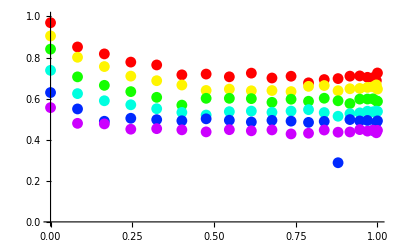

```mathematica
test=Table[{(i-1)/(resX-1),  paramsFlat0[[1]][[i]]},{i,1,resX}];
ListPlot[test];
valuesSn=Table[Table[{Cos[(i-1)/(resX-1)*π/2],paramsFlat0[[j]][[i]]},{i,1,resX}],{j,1,6}];
Show[Table[ListPlot[valuesSn[[i]],PlotRange->{0,1} , PlotStyle->Hue[0.16*(i-1)]],{i,1,6}]]
```

(a→0.699336 | b→0.264057 | c→5.28373
a→0.646501 | b→0.2611 | c→6.07679
a→0.591226 | b→0.247842 | c→8.32299
a→0.533366 | b→0.201661 | c→8.34108
a→0.473773 | b→0.150725 | c→7.78062
a→0.441773 | b→0.111167 | c→9.40142)

(0.699336+0.264057 ⅇ^(-5.28373 u)
0.646501+0.2611 ⅇ^(-6.07679 u)
0.591226+0.247842 ⅇ^(-8.32299 u)
0.533366+0.201661 ⅇ^(-8.34108 u)
0.473773+0.150725 ⅇ^(-7.78062 u)
0.441773+0.111167 ⅇ^(-9.40142 u))

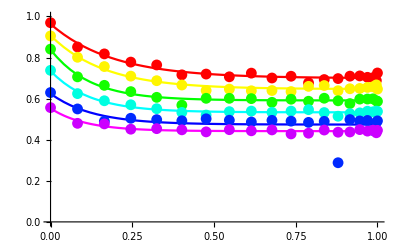

```mathematica
modelSn=a+b*Exp[-c * u];
fittingSn = Table[FindFit[ valuesSn[[j]],modelSn,{a,b,c},u ],{j,1,6}];
MatrixForm[fittingSn]
MatrixForm[modelSn/.fittingSn]
Show[Table[Plot[modelSn/.fittingSn[[j]],{u,0,1},PlotRange->{0,1},PlotStyle->Hue[(j-1)/6]],{j,1,6}],
Table[ListPlot[valuesSn[[i]],PlotRange->{0,1} , PlotStyle->Hue[0.16*(i-1)]],{i,1,6}]]
```

#### Matching Parameters

Now that we have a bunch of nice expressions for representing f(cos(θ)), we need to find tendencies in the fitted parameters a, b and c.

0.697462-0.479278 x

0.287646-0.293594 x

5.69744+6.61321 x

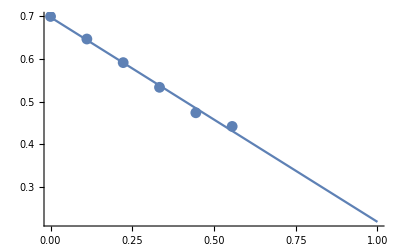

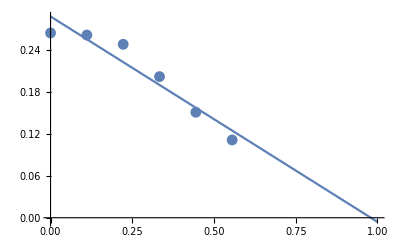

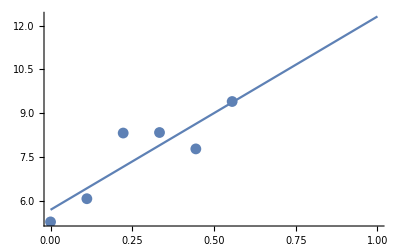

```mathematica
fa = Table[{(j-1)/9,a/.fittingSn[[j]]}, {j,1,6}];
fb = Table[{(j-1)/9,b/.fittingSn[[j]]}, {j,1,6}];
fc= Table[{(j-1)/9,c/.fittingSn[[j]]}, {j,1,6}];
mfa = LinearModelFit[fa,x,x];
mfb = LinearModelFit[fb,x,x];
mfc = LinearModelFit[fc,x,x];
Normal[mfa]
Normal[mfb]
Normal[mfc]
Show[ListPlot[fa,PlotRange->{0,1}],Plot[mfa[x],{x,0,1}],PlotRange->All]
Show[ListPlot[fb,PlotRange->{0,1}],Plot[mfb[x],{x,0,1}],PlotRange->All]
Show[ListPlot[fc,PlotRange->{0,10}],Plot[mfc[x],{x,0,1}],PlotRange->All]
```

#### Final Expression

We can now obtain the final expression for the function matching the lobe flattening factor:

a(ρ) = 0.697462 - 0.479278 ρ
b(ρ) = 0.287646 - 0.293594 ρ
c(ρ) = 5.69744 + 6.61321 ρ
μ = cos(θ)
f( μ, ρ ) = a(ρ) + b(ρ) e^(-c(ρ)  μ)

```mathematica
a[ρ_] = 0.697462 - 0.479278 ρ;
b[ρ_] = 0.287646 - 0.293594 ρ;
c[ρ_] = 5.69744 + 6.61321 ρ;
f[ μ_, ρ_] = a[ρ] + b[ρ] Exp[-c[ρ]  μ];

Plot3D[f[μ,ρ],{μ,0,1},{ρ,0,1},PlotRange->{0,1},AxesLabel->{"cos(θ)","ρ","Lobe Flattening"}]
```

-Graphics3D-

#### Checking our Matching

```mathematica
Show[
ListPlot3D[ paramsFlat0,PlotRange->{0,1},AxesLabel->{"θ","ρ"},PlotStyle->Blue],
Plot3D[f[Cos[(i-1)/(resX-1)π/2],(j-1)/(resY-1)],{i,1,resX},{j,1,resY},PlotStyle->Red]
]
```

-Graphics3D-

Pretty good! 
Now we can remove that parameter from the simulation and use our fitting instead. That should help us stabilize the other parameters...

Matching Masking Importance

```mathematica
paramsMask0 = Table[table0[[j]][[i]][[5]],{j,1,resY},{i,1,resX}];
paramsMask1 = Table[table1[[j]][[i]][[5]],{j,1,resY},{i,1,resX}];
paramsMask2 = Table[table2[[j]][[i]][[5]],{j,1,resY},{i,1,resX}];
paramsMask3 = Table[table3[[j]][[i]][[5]],{j,1,resY},{i,1,resX}];
```

```mathematica
ListPlot3D[paramsMask0,{ PlotRange->{0,0.25},AxesLabel->{"θ","ρ"}}]
ListPlot3D[paramsMask1,{ PlotRange->{0,0.25},AxesLabel->{"θ","ρ"}}]
ListPlot3D[paramsMask2,{ PlotRange->{0,1},AxesLabel->{"θ","ρ"}}];
ListPlot3D[paramsMask3,{ PlotRange->{0,1},AxesLabel->{"θ","ρ"}}];
```

-Graphics3D-

-Graphics3D-